## Observational approaches Ch 9

```mathematica
SetDirectory[NotebookDirectory[]];Get["Packages\\TextbookFigurePreamble.wl"] (* loads libraries, textbook stylings and defines txbExport *)
```

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
Get["LatticePhyllotaxis`",Path->FileNameJoin[githubPath,"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
Get["DiskStacking`",Path->FileNameJoin[githubPath,"GeometricalPhyllotaxis\\Mathematica\\Packages"]];
Get["TextbookStylings.m",Path->FileNameJoin[githubPath,"MathematicalPhyllotaxis\\Mathematica\\Packages"]];
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jFont[size_] := Directive[FontFamily->jStyle["FontFamily"],FontSize->size];
```

## Data

```mathematica
upto55=Import["upto55.mx",Path->FileNameJoin[githubPath,"MathematicalPhyllotaxis\\Mathematica\\Data"]];
```

## Txb1003InhibitionBoundary

## Txb1004NonopposedNo

```mathematica
txbExport@Txb1004NonopposedNo
```

Txb1004NonopposedNo

## Txb1005DGParastichy

```mathematica
txbExport@Txb1005DGParastichy
```

Txb1005DGParastichy

## Txb1006DeterministicTransition

```mathematica
txbExport@Txb1006DeterministicTransition
```

Txb1006DeterministicTransition

### fig : scpDeterministicTransition

### Graphics shows

```mathematica
chainLines[run_,chainNumber_] := Module[{w},
w=run;
w["ContactGraph"]=run["RunChains"][chainNumber]["Chain"];
graphToContactLines[w,leftRightColours]
];

chainLineThickness= AbsoluteThickness[2];
contactLineThickness= AbsoluteThickness[.5];
```

```mathematica
scpExplain[run_,zRange_,toShow_,chainNumbers_,stackedDiskNumber_,chain_] := Module[{diskNumbers,disks,ffs,cylinder,stackedDisks,stackedRun,nextDisk,contacts,cylinderLU,diskDisks,diskShow,ghainLines,chainBox,g},
ffs= Directive[FaceForm[White],EdgeForm[Black]];
diskNumbers = DiskStacking`diskNumbersInRun[run];
disks =Association@Map[#->DiskStacking`getDiskFromRun[run,#]&,
diskNumbers];
If[MissingQ[stackedDiskNumber],
stackedDisks=disks;stackedRun=run;nextDisk=Nothing[];
,
stackedDisks=KeySelect[disks,#<= stackedDiskNumber&];
stackedRun= DiskStacking`pruneRunByDisks[run,{0,stackedDiskNumber}];
nextDisk =  disks[stackedDiskNumber+1]
];



cylinderLU = zRange;
cylinder = {jStyle["ParastichyColour"][3],Rectangle[{-1/2,cylinderLU[[1]]},{1/2,cylinderLU[[2]]}]};

diskDisks=Map[DiskStacking`diskAndVisibleCopies,Values@stackedDisks];
If[!MemberQ[toShow,"Circles"] || MemberQ[toShow,"Disks"],
diskShow= {}];
If[MemberQ[toShow,"Disks"],
diskShow={Directive[FaceForm[White],EdgeForm[None]],diskDisks}];
If[MemberQ[toShow,"Circles"],
diskShow={Directive[FaceForm[None],EdgeForm[Black]],diskDisks}];
If[MemberQ[toShow,"Circles"] && MemberQ[toShow,"Disks"],
diskShow={Directive[FaceForm[White],EdgeForm[Black]],diskDisks}];

contacts = graphToContactLines[stackedRun,leftRightColours];
ghainLines=Map[chainLines[run,#]&,chainNumbers];

chainBox = If[MissingQ[chain],Nothing[],{FaceForm[{Opacity[0.5],Gray}],EdgeForm[None],chainRectangle[chain]}];

g=Graphics[{
cylinder
,
diskShow
,{
{contactLineThickness,If[MemberQ[toShow,"Contacts"],contacts,Nothing[]]}}
,chainLineThickness,ghainLines
,{FaceForm[jParastichyColour[1]],EdgeForm[None],nextDisk}
,chainBox 
}
,Axes->False,PlotRangeClipping->True
,PlotRange->{{-1/2,1/2},cylinderLU}
]

];
```

```mathematica
graphToContactLines[run_,leftRightColours_] := graphToContactLines[run["ContactGraph"],run,leftRightColours];

graphToContactLines[g_,run_,leftRightColours_] := Module[{dlines,fsort,res},
dlines = Line/@Map[diskXZ[getDiskFromRun[run,#]]&,List@@@EdgeList[g],{2}];fsort[Line[{p1_,p2_}]] := If[First[p1]<First[p2],Line[{p1,p2}],Line[{p2,p1}]];dlines=Map[fsort,dlines];res = lineCylinderIntersectionColoured[#,leftRightColours]& /@dlines;
res
];


lineCylinderIntersectionColoured[Line[{{x1_,z1_},{x2_,z2_}}],leftRightColours_] :=
 Module[{slope,col},
slope= (z2-z1)/(x2-x1);
If[slope>0,col=leftRightColours["Left"],col=leftRightColours["Right"]];If[x1<-1/2,Return[
{col,
Line[{{-1/2, z2 - slope * (x2-(-1/2))},{x2,z2}}], Line[{{x1+1,z1},{1/2,z1+slope *( 1/2-(1+x1))}}]
}
]];
If[x2>1/2,Return[
{col,
Line[{{-1/2, z2- slope * (x2-1-(-1/2))},{x2-1,z2}}], Line[{{x1,z1},{1/2,z1+slope *( 1/2-(x1))}}]
}
]];
Return[{col,Line[{{x1,z1},{x2,z2}}]}] 
];
(*
diskAndVisibleCopies[Disk[{x_,z_},r_]] := {Disk[{x,z},r],If[x+r>1/2,moveDiskLeft[Disk[{x,z},r]],Nothing[]],If[x-r<-1/2,moveDiskRight[Disk[{x,z},r]],Nothing[]]};
*)
```

```mathematica
showZBar=False;

grainLines[run_,col_,zRange_,toShow_,chain_:Missing[],zBarRange_:Missing[]] := Module[{red,g,zTransitionRange,zBar,chainBox,centres,centrePoints},

(*zTransitionRange= Values[KeyTake[run["Arena"],{"rFixedBefore","rFixedAfter"}]];
*)
If[!Missing[zBarRange],
showZBar,zBar= {FaceForm[Gray],EdgeForm[None],Opacity[0.2],Rectangle[{-1/2,zBarRange[[1]]},{1/2,zBarRange[[2]]}]},zBar=Nothing[]];

g=graphToContactLines[run,leftRightColours];
chainBox = If[MissingQ[chain],Nothing[],{FaceForm[{Opacity[0.5],Gray}],EdgeForm[None],chainRectangle[chain]}];
centres= If[MemberQ[toShow,"Centres"],Map[DiskStacking`diskXZ[#Disk]&,Values[run["DiskData"]]],{}];
centrePoints= {PointSize[Small],Point[centres,VertexColors->White]};
centrePoints= Map[Inset[Graphics[{FaceForm[White],EdgeForm[None],Disk[]}],#,Center,0.005]&,centres];
red=Select[g,First[#]==col&];
Graphics[{zBar,contactLineThickness,red,centrePoints,chainBox},Axes->False,PlotRangeClipping->True
,PlotRange->{{-1/2,1/2},zRange}]
]

chainRectangle[chain_] := Rectangle @@{{-1/2,#[[1]]},{1/2,#[[2]]}}&@ MinMax@Map[AnnotationValue[{chain,#},VertexCoordinates][[2]]&,VertexList[chain]];

scpShowGrain[run_,zRange_,toShow_,mostRecentDisk_] := Module[{chain},
chain=run["RunChains"][mostRecentDisk]["Chain"];
GraphicsGrid[{{
panelInset[scpExplain[run,zRange,toShow,{mostRecentDisk},mostRecentDisk,chain],"a"]
,
panelInset[scpExplain[run,zRange,toShow,{},Missing[],chain],"b"]
},{
panelInset[grainLines[run,jParastichyColour[1],zRange,toShow,chain],"c"]
,
panelInset[grainLines[run,jParastichyColour[2],zRange,toShow,chain],"d"]
}}
]
];

panelInset[panel_,label_] := Show[panel,Graphics[Inset[Style[label,jFont[Scaled[.1]]],Scaled[{0,1}],Scaled[{0,1}],Background->White]]];
```

```mathematica
(* rcp-upto55 generated by stackedcoinpaper code 
upto55= getRunByTag["rcp-upto55-solo1"]["Run"];
SetDirectory[NotebookDirectory[]];Export["upto55.mx",upto55]
*)
```

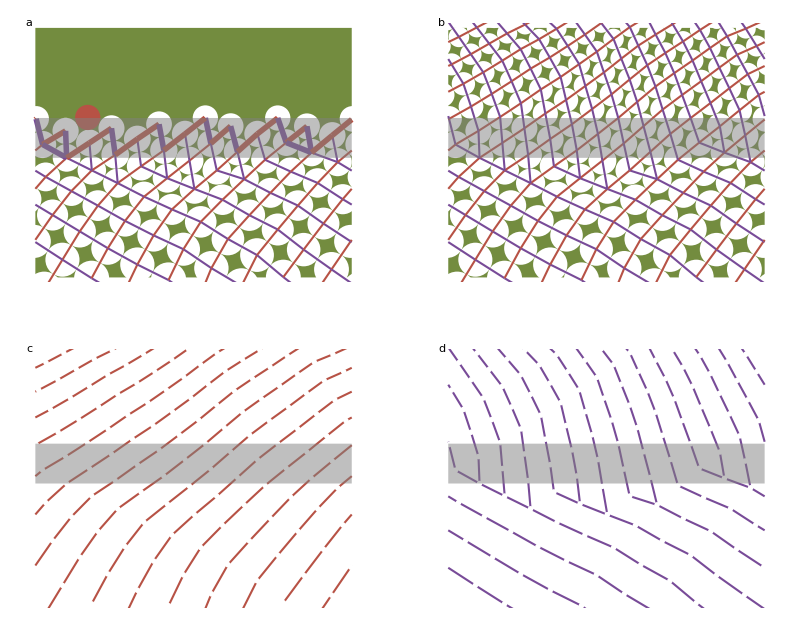

```mathematica
chainLineThickness= AbsoluteThickness[4];
contactLineThickness= AbsoluteThickness[1.5];
pun = DiskStacking`pruneRun[upto55,{14.75,15.7}];
cylinderLU={14.75,15.7}+{0.08,-0.08};

Txb1006DeterministicTransition = scpShowGrain[pun,cylinderLU,{"Disks","Contacts","Centres"},199]
```

```mathematica
jExport[scpDeterministicTransition]
```

-Graphics-

```mathematica
txbExport@Txb1003InhibitionBoundary
```

Txb1003InhibitionBoundary

## Txb1007ParastichyCountsTo89

```mathematica
txbExport@Txb1007ParastichyCountsTo89
```

Txb1007ParastichyCountsTo89

## Txb1008FixedRadius

```mathematica
txbExport@Txb1008FixedRadius
```

Txb1008FixedRadius

## Txb1009AreaTimeSeries

```mathematica
txbExport@Txb1009AreaTimeSeries
```

Txb1009AreaTimeSeries

## Txb1010Tilings

```mathematica
txbExport@Txb1010Tilings
```

Txb1010Tilings

## Txb1012TransitionLattices

```mathematica
txbExport@Txb1012TransitionLattices
```

Txb1012TransitionLattices

## Txb1013AhaPair

```mathematica
txbExport@Txb1013AhaPair
```

Txb1013AhaPair

## Txb1014ConeTransformation

```mathematica
txbExport@Txb1014ConeTransformation
```

Txb1014ConeTransformation

## Txb1015Falling

```mathematica
txbExport@Txb1015Falling
```

Txb1015Falling